```mathematica
boat=ImplicitRegion[y<10.&&y>8./(z^1.2) *x^2.+1./1.3*(z-29.)^2./200.&&0.<z<57.,{x,y,z}]
Region[boat,PlotTheme->"Scientific",AxesLabel->{x,y,z}]
```

ImplicitRegion[y<10.&&y>0.00384615 (-29.+z)^2.+(8. x^2.)/z^1.2&&0.<z<57.,{x,y,z}]

-Graphics3D-

```mathematica
top=ImplicitRegion[57.>z>.5*x^2.&&9.9<=y<18.,{x,y,z}]
Region[top,PlotTheme->"Scientific",AxesLabel->{x,y,z}]
```

ImplicitRegion[57.>z>0.5 x^2.&&9.9≤y<18.,{x,y,z}]

-Graphics3D-

```mathematica
Show[Region[top,PlotTheme->"Scientific",AxesLabel->{x,y,z}],Region[boat,PlotTheme->"Scientific",AxesLabel->{x,y,z}]]
```

-Graphics3D-

```mathematica
Clear[fullBoat];
discreteBoat=DiscretizeRegion[boat];
discreteTop=DiscretizeRegion[top];
(*fullBoat=RegionIntersection[boat,top]*)
(*fullBoatDiscrete=RegionUnion[discreteBoat,discreteTop]
*)
```

This is the boat you want :

```mathematica
boat=ImplicitRegion[y<10.&&y>4./(z^1.2) *x^2.+.5*(z-29.)^2./200.&&0.<z<57.,{x,y,z}];
top=ImplicitRegion[57.>z>.2*x^2.&&9.9<=y<18.,{x,y,z}];
discreteBoat=DiscretizeRegion[boat];
discreteTop=DiscretizeRegion[top];
fullBoatDiscrete=RegionUnion[discreteBoat,discreteTop];
Region[fullBoatDiscrete,PlotTheme->"Scientific",AxesLabel->{x,y,z}]
```

BoundaryMeshRegion::bsuncl: The boundary surface is not closed because the edges Line[{{1827,1828},{815,816},{3707,3703},{3662,3663},{1370,1372},{2399,2397},{8,1803},{57,59},{1951,2371},{25,27},{2881,2880},{3726,3725},{858,854},{1817,1818},{11,18},«21»,{1376,1377},{2522,2527},{1799,1801},{2979,2977},{186,184},{55,57},{1267,1270},{2642,2639},{411,390},{3408,3409},{1524,3357},{1419,1409},{3709,3995},{2449,2450},«385»}] only come from a single face.

-Graphics3D-

ImplicitRegion::bcond: … should be a Boolean combination of equations, inequalities, and Element statements.

ImplicitRegion[fullBoatDiscrete/.{z→5},{x,y,z}]

Region::reg: ImplicitRegion[fullBoatDiscrete/.{z→5},{x,y,z}] is not a correctly specified region.

Region[ImplicitRegion[fullBoatDiscrete/.{z→5},{x,y,z}]]

```mathematica
ztesttop=ImplicitRegion[57.>z>.2*x^2.&&9.9<=y<18.,{x,y}]
ztestboat=ImplicitRegion[y<10.&&y>4./(z^1.2) *x^2.+.5*(z-29.)^2./200.,{x,y}]
```

ImplicitRegion[57.>z>0.2 x^2.&&9.9≤y<18.,{x,y}]

ImplicitRegion[y<10.&&y>0.0025 (-29.+z)^2.+(4. x^2.)/z^1.2,{x,y}]

ImplicitRegion[(1. x^2.<110.&&9.9≤y<18.)||(y<10.&&y>0.1225+0.0979835 x^2.),{x,y}]

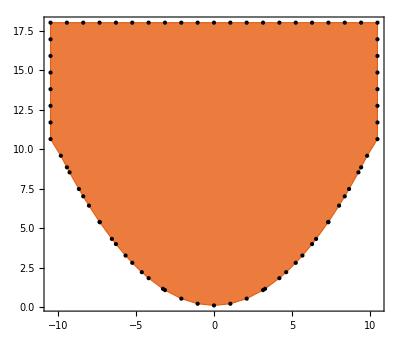

```mathematica
ztest=RegionUnion[ztesttop/.{z->22},ztestboat/.{z->22}]
Region[ztest,PlotTheme->"Scientific"]
```

```mathematica
RegionBounds[ztest]
```

{{-10.4881,10.4881},{0.1225,18.}}

ImplicitRegion[y<10.&&y>0.0025 (-29.+z)^2.+(4. x^2.)/z^1.2,{y,z}]

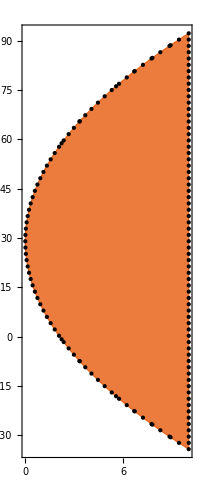

```mathematica
xtestboat=ImplicitRegion[y<10.&&y>4./(z^1.2) *x^2.+.5*(z-29.)^2./200.,{y,z}]
Region[xtestboat/.x->0,PlotTheme->"Scientific"]
```